```mathematica
Clear["Global*`"]
```

Plotting zeros of a single harmonic polynomial

This code takes as input two arbitrary complex analytic polynomials, p[z] and q[z]. 
 It then constructs the harmonic polynomial h[z]=p[z]+Conjugate[q[z]].  
 It uses NSlove to find the zeros of h[z] and then plots the zeros in the complex plane along with the unit circle.

{0,-1.22474-1.22474 ⅈ,-1.22474+1.22474 ⅈ,1.22474-1.22474 ⅈ,1.22474+1.22474 ⅈ,-3.-4.89898 ⅈ,-3.+4.89898 ⅈ,-11.7446,-0.255437}

There are 9 zeros of h[z]

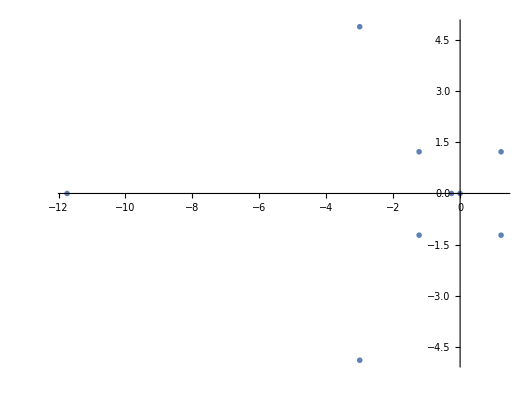

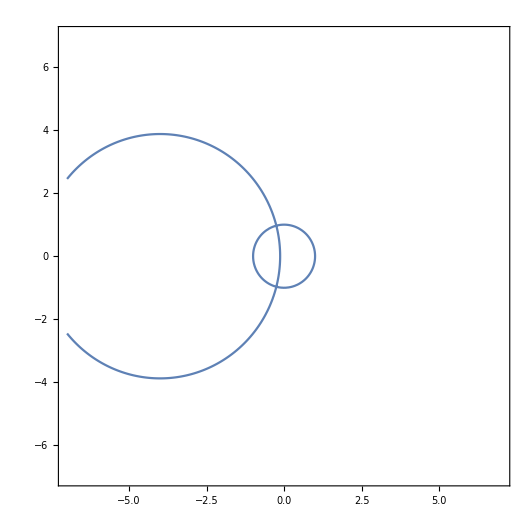

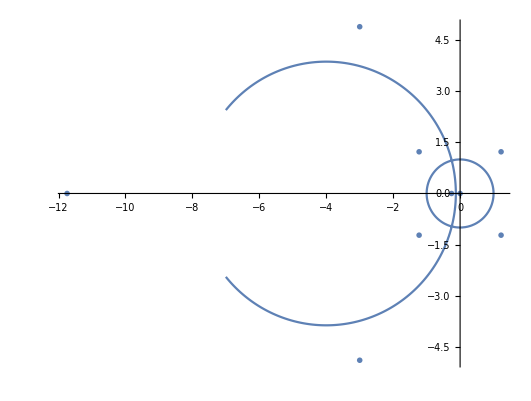

```mathematica
Clear["Global*`"];
(* Circles family *)

A =2;
n = 3;
p[z_]=z+A*z^2;  (* p[z] can be any analytic polynomial *)
q[z_]=2*A(z^(n-1))/(n-1)+(z^n)/n; (* q[z] can be any analytic polynomial *)


(*Traditional family *)
(*
A = 1;
B = 1;
n = 7;
k = 6;
p[z_]=A*z^n+z;  (* p[z] can be any analytic polynomial *)
q[z_]=B*z^k; (* q[z] can be any analytic polynomial *)
*)

DGraphHalfInteralLength = 7;


DerP[z_]=p'[z];
DerQ[z_]=q'[z];
PDerP[x_,y_]= DerP[x+I*y];
PDerQ[x_,y_] = DerQ[x+I*y];
h[z_]=p[z]+Conjugate[q[z]];


zeros=NSolve[h[z]==0, z];
zeros=Flatten[zeros];
zeros=zeros[[All, 2]]
Print[" There are ", Length[zeros], " zeros of h[z]"]
ZerosPlot=ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@zeros, PlotStyle->PointSize[.02],AspectRatio->Automatic,PlotMarkers->{-Graphics3D-,Offset[15]}]
DilitationPlot=ContourPlot[Abs[PDerP[x,y]]== Abs[PDerQ[x,y]],{x,-DGraphHalfInteralLength,DGraphHalfInteralLength},{y,-DGraphHalfInteralLength,DGraphHalfInteralLength}, PlotPoints->100] 
Show[ZerosPlot,DilitationPlot,AspectRatio->Automatic]
```

Image of Plane Under Harmonic Function

This code allows the user to input a polynomial they wish to see the grid lines transformed under. It uses contour plot to plot the real part of h[x+Iy] in red and the imaginary part in grey.

2 z^4

z+z^5+2 Conjugate[z]^4

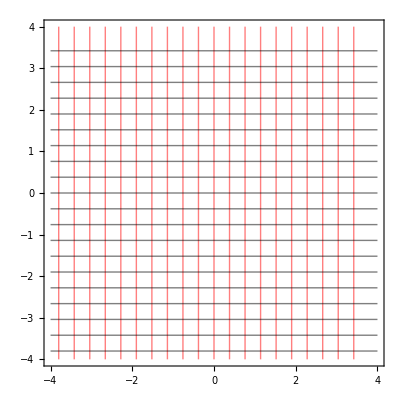

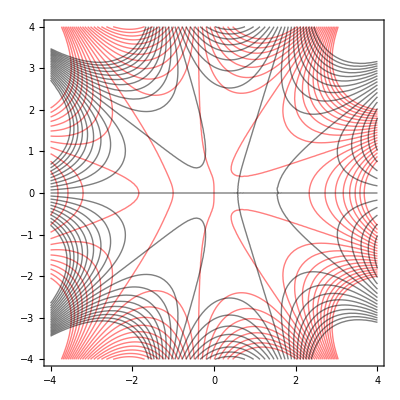

```mathematica
Clear["Global*`"]
p[z_]=z^5+z;  
q[z_]=2*z^4 
h[z_]=p[z] + Conjugate[q[z]] (* the polynomial you wish to see grid lines transformed under *)
XYMIN =-4;
XYMAX = 4;
CONTOURNUMBER = 20;


UnTransformedPic =Show[ContourPlot[Re[x+I*y],{x,XYMIN,XYMAX},{y,XYMIN,XYMAX},ContourShading->False, Contours->CONTOURNUMBER,ContourStyle->Red],ContourPlot[Im[x+I*y],{x,XYMIN,XYMAX},{y,XYMIN,XYMAX},ContourShading->False,Contours->CONTOURNUMBER],AspectRatio->Automatic,ImageSize->400]
TransformedPic=Show[ContourPlot[Re[h[x+I*y]],{x,XYMIN,XYMAX},{y,XYMIN,XYMAX},ContourShading->False, Contours->CONTOURNUMBER, ContourStyle->Red],ContourPlot[Im[h[x+I*y]],{x,XYMIN,XYMAX},{y,XYMIN,XYMAX},ContourShading->False, Contours->CONTOURNUMBER],AspectRatio->Automatic,ImageSize->400]
```

Image of Concentric Circles Under Harmonic Function (Polar Form)

This code allows the user to input a harmonic polynomial they wish to see the concentric circles transformed under. It uses Polar Plot to plot the modulus of the output of our harmonic polynomial in polar coordinates.

Syntax::sntxi: Incomplete expression; more input is needed .

2 z^4

z+z^5+2 Conjugate[z]^4

1

0.1

24

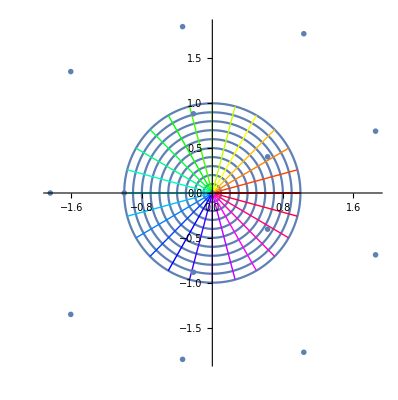

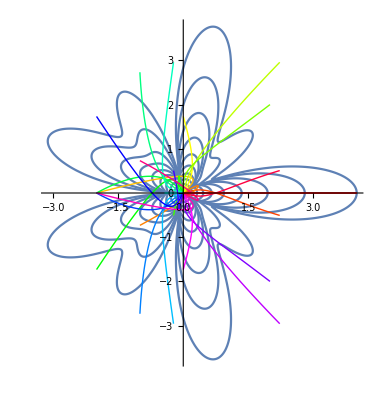

```mathematica
Clear["Global*`"]
p[z_]=z^5+z;  
q[z_]=2*z^4 
h[z_]=p[z] + Conjugate[q[z]] 
(* the polynomial you wish to see the circles transformed under *)
RMIN = 0;
RMAX = 1
RSTEPSIZE = .1
ArrowCount = 24

Zeros=NSolve[h[z]==0, z];
Zeros=Flatten[Zeros];
Zeros=Zeros[[All, 2]];
ZeroGraph=ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Zeros, PlotStyle->PointSize[.02],AspectRatio->Automatic,PlotMarkers->{-Graphics3D-,Offset[15]}];


Show[PolarPlot[#,{theta,0,2Pi}]&/@Range[RMIN,RMAX,RSTEPSIZE],ParametricPlot[{{R*Cos[#],R*Sin[#]}},{R,0,RMAX},PlotStyle->{Hue[#/(2*Pi)],Thick}]&/@Range[0,2*Pi,2*Pi/ArrowCount],ZeroGraph,PlotRange->All]


Show[PolarPlot[Abs[h[#*E^(I*theta)]],{theta,0,2Pi}]&/@Range[RMIN,RMAX,RSTEPSIZE],ParametricPlot[{{Re[h[R*E^(I*#)]],Im[h[R*E^(I*#)]]}},{R,0,RMAX},PlotStyle->{Hue[#/(2*Pi)],Thick}]&/@Range[0,2*Pi,2*Pi/ArrowCount], PlotRange->All]

(* If you want just the Rayw under the function uncomment the following code *)

(* Show[ParametricPlot[{{Re[h[R*E^(I*#)]],Im[h[R*E^(I*#)]]}},{R,0,RMAX},PlotStyle->{Hue[#/(2*Pi)],Thick}]&/@Range[0,2*Pi,2*Pi/ArrowCount],PlotRange->All] *)

(* If you want each radius increment shown to you uncomment the following code *)

 (* PolarPlot[Abs[h[#*E^(I*theta)]],{theta,0,2Pi}, PlotLabel->"Radius" #]&/@Range[RMIN,RMAX,RSTEPSIZE] *)
```